```mathematica
(*https://reference.wolfram.com/language/howto/SolveADifferentialEquation.html*)
Clear["Global`*"];
DSolve[y''[x]==-(a+2*ϵ*Cos[x])*x,y[x],x]
```

{{y[x]→-(a x^3)/6+C[1]+x C[2]+2 x ϵ Cos[x]-4 ϵ Sin[x]}}

```mathematica
(*For y[0]=0 and y'[0]=0*)
-(a x^3)/6-2*ϵ+4*ϵ*x +2 x ϵ Cos[x]-4 ϵ Sin[x]
```

{0.-x^3/6,-0.2+0.4 x-x^3/6+0.2 x Cos[x]-0.4 Sin[x],-1.6+3.2 x-x^3/6+1.6 x Cos[x]-3.2 Sin[x],-5.4+10.8 x-x^3/6+5.4 x Cos[x]-10.8 Sin[x],-12.8+25.6 x-x^3/6+12.8 x Cos[x]-25.6 Sin[x],-25.+50. x-x^3/6+25. x Cos[x]-50. Sin[x],-43.2+86.4 x-x^3/6+43.2 x Cos[x]-86.4 Sin[x],-68.6+137.2 x-x^3/6+68.6 x Cos[x]-137.2 Sin[x],-102.4+204.8 x-x^3/6+102.4 x Cos[x]-204.8 Sin[x],-145.8+291.6 x-x^3/6+145.8 x Cos[x]-291.6 Sin[x]}

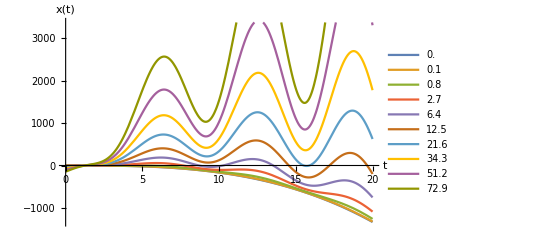

```mathematica
iMin=0;
iMax=10;
iStep=0.1;
tMax=20;
AList={};(*A list of epsilon/a*)
FunctionList={};
For[i=iMin,i<iMax,i++,
ϵ=iStep*i^3;
(*Print[ϵ];*)
function=-x^3/6-2*ϵ+4*ϵ*x +2 x ϵ Cos[x]-4 ϵ Sin[x];
(*Print[function];*)
AppendTo[FunctionList,function];
AppendTo[AList,ϵ]

]
Print[FunctionList]

Plot[FunctionList,{x,0,tMax},
AxesLabel->{Style[ToExpression["t",TeXForm,HoldForm
]
,Bold,20],
Style[ToExpression["x[t]",TeXForm,HoldForm
]
,Bold,20]},
PlotLegends->AList
]
```